```mathematica
S[x_]:=Exp[-Abs[x]/2]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1+ϵ,Subscript[L, 1]->1+ϵ}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 1] Subscript[k, w][x,ξ]-Subscript[c, 0] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[L, 0]},Assumptions->ξ<Subscript[L, 0]<0]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[L, 0]},Assumptions->ξ<Subscript[L, 0]<0]
Subscript[F, 0][ξ_]=Expand[Subscript[T, 0][ξ]/.var];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[M Subscript[c, 3] Subscript[k, l][x,ξ]-Subscript[c, 2] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-Limit[M Subscript[c, 1] Subscript[k, l][x,ξ]-Subscript[c, 0] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[L, 1]},Assumptions->Subscript[L, 0]<ξ<Subscript[L, 1]]+Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[L, 1]},Assumptions->{Subscript[L, 0]<ξ<Subscript[L, 1],Subscript[L, 0]<0,Subscript[L, 1]>0}]
Subscript[F, 1][ξ_]=Refine[Expand[Subscript[T, 1][ξ]/.var],{0≤ϵ<1,Subscript[L, 0]<ξ<Subscript[L, 1]}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=-Limit[Subscript[c, 3] Subscript[k, w][x,ξ]-Subscript[c, 2] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],∞},Assumptions->ξ>Subscript[L, 1]>0]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],∞},Assumptions->ξ>Subscript[L, 1]>0]
Subscript[F, 2][ξ_]=Expand[Subscript[T, 2][ξ]/.var];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[L, 0]]-Subscript[F, 1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 1]=Subscript[F, 2][Subscript[L, 1]]-Subscript[F, 1][Subscript[L, 1]]==0/.var;
Subscript[eqn, 2]=M Subscript[F, 0]'[Subscript[L, 0]]-Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 3]=M Subscript[F, 2]'[Subscript[L, 1]]-Subscript[F, 1]'[Subscript[L, 1]]==0/.var;
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=400;
Subscript[Q, max]=600;
n=2(Subscript[Q, max]-Subscript[Q, min])+1;
Subscript[ϵ, test]=0.001;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],ϵ->Rationalize[Subscript[ϵ, test],0]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0}}/.tempQ,MaxIterations->100,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
conds=Quiet[NMaxValue[{Subscript[F, 0][x],-10<x<Subscript[L, 0]}/.sol,x]<-0.99999&&
NMaxValue[{Subscript[F, 1][x],Subscript[L, 0]<x<Subscript[L, 1]}/.sol,x]<0.00001&&
NMaxValue[{Subscript[F, 2][x],Subscript[L, 1]<x<10}/.sol,x]<-0.99999/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x]/.sol,x<Subscript[L, 0]/.sol},{Subscript[F, 1][x]/.sol,Subscript[L, 0]≤x≤Subscript[L, 1]/.sol},{Subscript[F, 2][x]/.sol,Subscript[L, 1]<x/.sol}}],0];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],N[M[ϵ]/.sol],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["C:\\masterA GitHub\\Code\\Exponential\\Continent Offset 0.001\\1 - IceSnowIce.csv",sols,Format->Table];
```

-0.83

-1.

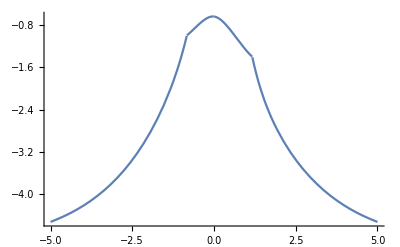

```mathematica
tempQ={Q->Rationalize[536.6155094919433],ϵ->0.17};
sol=NSolve[{Subscript[eqn, 0]/.tempQ,Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ},{Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}];
sol=Join[tempQ,sol[[1]],var/.tempQ];
M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x]/.sol,x<Subscript[L, 0]/.sol},{Subscript[F, 1][x]/.sol,Subscript[L, 0]≤x≤Subscript[L, 1]/.sol},{Subscript[F, 2][x]/.sol,Subscript[L, 1]<x/.sol}}],0];
NArgMax[{M[x],x<Subscript[L, 0]/.sol},x]
NMaxValue[{M[x],x<Subscript[L, 0]/.sol},x]
Plot[M[x],{x,-5,5},WorkingPrecision->20]
```